```mathematica
Quiet@Needs["MagneticTB`"];
```

```mathematica
SystemOpen[FileNameJoin[{$UserBaseDirectory,"Applications"}]]
```

### Three-band tight-binding model for MoS2

```mathematica
sgop=msgop[gray[187]];
tran={{1,-1,0},{0,1,0},{0,0,1}};
sgoptr=MapAt[FullSimplify[tran.#.Inverse@tran]&,sgop,{;;,2}];

init[
lattice->{{1,0,0},{1/2,(√3)/2,0},{0,0,100}},
lattpar->{},
wyckoffposition->{{{0,0,0},{0,0,0}}},
symminformation->sgoptr,
basisFunctions->{{"dz2","dxy","dx2-y2"}}];
```

Magnetic space group (BNS): {187.210,P-6m21'}

Lattice: HexagonalP

Primitive Lattice Vactor: {{a,0,0},{-a/2,(√3 a)/2,0},{0,0,c}}

Conventional Lattice Vactor: {{a,0,0},{-a/2,(√3 a)/2,0},{0,0,c}}

```mathematica
mos2=Sum[symham[i,symmetryset->{9,11,13}],{i,{1,2}}];MatrixForm[ExpToTrig[mos2]]
```

params:{e1,e2}

params:{t1,t2,t3,t4,t5,t6}

(e1+2 t1 Cos[kx]+2 t1 Cos[kx-ky]+2 t1 Cos[ky] | -√3 t4 Cos[kx-ky]+√3 t4 Cos[ky]+2 ⅈ t2 Sin[kx]+ⅈ t2 Sin[kx-ky]+ⅈ t2 Sin[ky] | 2 t4 Cos[kx]-t4 Cos[kx-ky]-t4 Cos[ky]-ⅈ √3 t2 Sin[kx-ky]+ⅈ √3 t2 Sin[ky]
-√3 t4 Cos[kx-ky]+√3 t4 Cos[ky]-2 ⅈ t2 Sin[kx]-ⅈ t2 Sin[kx-ky]-ⅈ t2 Sin[ky] | e2+2 t3 Cos[kx]+1/2 t3 Cos[kx-ky]+3/2 t6 Cos[kx-ky]+1/2 t3 Cos[ky]+3/2 t6 Cos[ky] | -1/2 √3 t3 Cos[kx-ky]+1/2 √3 t6 Cos[kx-ky]+1/2 √3 t3 Cos[ky]-1/2 √3 t6 Cos[ky]+2 ⅈ t5 Sin[kx]-2 ⅈ t5 Sin[kx-ky]-2 ⅈ t5 Sin[ky]
2 t4 Cos[kx]-t4 Cos[kx-ky]-t4 Cos[ky]+ⅈ √3 t2 Sin[kx-ky]-ⅈ √3 t2 Sin[ky] | -1/2 √3 t3 Cos[kx-ky]+1/2 √3 t6 Cos[kx-ky]+1/2 √3 t3 Cos[ky]-1/2 √3 t6 Cos[ky]-2 ⅈ t5 Sin[kx]+2 ⅈ t5 Sin[kx-ky]+2 ⅈ t5 Sin[ky] | e2+2 t6 Cos[kx]+3/2 t3 Cos[kx-ky]+1/2 t6 Cos[kx-ky]+3/2 t3 Cos[ky]+1/2 t6 Cos[ky])

```mathematica
mos2=Sum[symham[i,symmetryset->All],{i,2}];MatrixForm[ExpToTrig[mos2]]
```

params:{e1,e2}

params:{t1,t2,t3,t4,t5,t6}

(e1+2 t1 Cos[kx]+2 t1 Cos[kx-ky]+2 t1 Cos[ky] | -√3 t4 Cos[kx-ky]+√3 t4 Cos[ky]+2 ⅈ t2 Sin[kx]+ⅈ t2 Sin[kx-ky]+ⅈ t2 Sin[ky] | 2 t4 Cos[kx]-t4 Cos[kx-ky]-t4 Cos[ky]-ⅈ √3 t2 Sin[kx-ky]+ⅈ √3 t2 Sin[ky]
-√3 t4 Cos[kx-ky]+√3 t4 Cos[ky]-2 ⅈ t2 Sin[kx]-ⅈ t2 Sin[kx-ky]-ⅈ t2 Sin[ky] | e2+2 t3 Cos[kx]+1/2 t3 Cos[kx-ky]+3/2 t6 Cos[kx-ky]+1/2 t3 Cos[ky]+3/2 t6 Cos[ky] | -1/2 √3 t3 Cos[kx-ky]+1/2 √3 t6 Cos[kx-ky]+1/2 √3 t3 Cos[ky]-1/2 √3 t6 Cos[ky]+2 ⅈ t5 Sin[kx]-2 ⅈ t5 Sin[kx-ky]-2 ⅈ t5 Sin[ky]
2 t4 Cos[kx]-t4 Cos[kx-ky]-t4 Cos[ky]+ⅈ √3 t2 Sin[kx-ky]-ⅈ √3 t2 Sin[ky] | -1/2 √3 t3 Cos[kx-ky]+1/2 √3 t6 Cos[kx-ky]+1/2 √3 t3 Cos[ky]-1/2 √3 t6 Cos[ky]-2 ⅈ t5 Sin[kx]+2 ⅈ t5 Sin[kx-ky]+2 ⅈ t5 Sin[ky] | e2+2 t6 Cos[kx]+3/2 t3 Cos[kx-ky]+1/2 t6 Cos[kx-ky]+3/2 t3 Cos[ky]+1/2 t6 Cos[ky])

```mathematica
mos2Liu=mos2/.Thread[{kx,ky,kz}->({kx,ky,kz}(2Pi)).Inverse@reclatt];
Expand@Simplify[ExpToTrig@mos2Liu/.{kx->2α,ky->2/√3 β,t1->T0,t4->T2,t2->T1,t3->T11,t6->T22,t5->T12}]//MatrixForm
```

(e1+2 T0 Cos[α]^2+4 T0 Cos[α] Cos[β]-2 T0 Sin[α]^2 | 4 ⅈ T1 Cos[α] Sin[α]+2 ⅈ T1 Cos[β] Sin[α]-2 √3 T2 Sin[α] Sin[β] | 2 T2 Cos[α]^2-2 T2 Cos[α] Cos[β]-2 T2 Sin[α]^2+2 ⅈ √3 T1 Cos[α] Sin[β]
-4 ⅈ T1 Cos[α] Sin[α]-2 ⅈ T1 Cos[β] Sin[α]-2 √3 T2 Sin[α] Sin[β] | e2+2 T11 Cos[α]^2+T11 Cos[α] Cos[β]+3 T22 Cos[α] Cos[β]-2 T11 Sin[α]^2 | 4 ⅈ T12 Cos[α] Sin[α]-4 ⅈ T12 Cos[β] Sin[α]-√3 T11 Sin[α] Sin[β]+√3 T22 Sin[α] Sin[β]
2 T2 Cos[α]^2-2 T2 Cos[α] Cos[β]-2 T2 Sin[α]^2-2 ⅈ √3 T1 Cos[α] Sin[β] | -4 ⅈ T12 Cos[α] Sin[α]+4 ⅈ T12 Cos[β] Sin[α]-√3 T11 Sin[α] Sin[β]+√3 T22 Sin[α] Sin[β] | e2+2 T22 Cos[α]^2+3 T11 Cos[α] Cos[β]+T22 Cos[α] Cos[β]-2 T22 Sin[α]^2)

```mathematica
path={{{{0,0,0},{2/3,1/3,0}},{"Γ","K"}},{{{2/3,1/3,0},{1/2,1/2,0}},{"K","M"}},{{{1/2,1/2,0},{0,0,0}},{"M","Γ"}}};
```

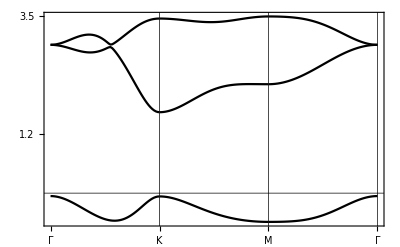

```mathematica
bandplot[path,60,mos2,{e1->1.046,e2->2.104,t1->-0.184,t2-> 0.401,t4-> 0.507,t3-> 0.218,t5-> 0.338,t6-> 0.057}]
```

```mathematica
init[
lattice->{{1,0,0},{1/2,(√3)/2,0},{0,0,100}},
lattpar->{},
wyckoffposition->{{{0,0,0},{0,0,0}}},
symminformation->sgoptr,
basisFunctions->{{"dz2up","dxyup","dx2-y2up","dz2dn","dxydn","dx2-y2dn"}}];
mos2soc=Quiet@Sum[symham[i,symmetryset->{9,11,13}],{i,1}];MatrixForm[ExpToTrig[mos2soc]]
```

Double Value Rep.

params:{e1,e2,e3}

(e2 | 0 | 0 | 0 | 0 | 0
0 | e3 | ⅈ e1 | 0 | 0 | 0
0 | -ⅈ e1 | e3 | 0 | 0 | 0
0 | 0 | 0 | e2 | 0 | 0
0 | 0 | 0 | 0 | e3 | -ⅈ e1
0 | 0 | 0 | 0 | ⅈ e1 | e3)

```mathematica
init[
lattice->{{1,0,0},{1/2,(√3)/2,0},{0,0,100}},
lattpar->{},
wyckoffposition->{{{0,0,0},{0,0,0}}},
symminformation->sgoptr,
basisFunctions->{{"dz2up","dz2dn","dxyup","dxydn","dx2-y2up","dx2-y2dn"}}];
mos2soc=Quiet@Sum[symham[i,symmetryset->{9,11,13}],{i,1}];MatrixForm[ExpToTrig[mos2soc]]
```

Double Value Rep.

params:{e1,e2,e3}

(e2 | 0 | 0 | 0 | 0 | 0
0 | e2 | 0 | 0 | 0 | 0
0 | 0 | e3 | 0 | ⅈ e1 | 0
0 | 0 | 0 | e3 | 0 | -ⅈ e1
0 | 0 | -ⅈ e1 | 0 | e3 | 0
0 | 0 | 0 | ⅈ e1 | 0 | e3)

### Graphene

```mathematica
sgop=msgop[gray[191]];
init[
lattice->{{a,0,0},{-(a/2),(Sqrt[3] a)/2,0},{0,0,c}},
lattpar->{a->1,c->3},
wyckoffposition->{{{1/3,2/3,0},{0,0,0}}},
symminformation->sgop,
basisFunctions->{{"pz"}}];
```

Magnetic space group (BNS): {191.234,P6/mmm1'}

Lattice: HexagonalP

Primitive Lattice Vactor: {{a,0,0},{-a/2,(√3 a)/2,0},{0,0,c}}

Conventional Lattice Vactor: {{a,0,0},{-a/2,(√3 a)/2,0},{0,0,c}}

```mathematica
TableForm[bondclassify[[#]],TableAlignments->Center,TableDepth->2,TableHeadings->{{"C1","C2"},{"Bond Lenth","Number of bonds","ATomic position"}}]&/@Range[5]//Column
```

| Bond Lenth | Number of bonds | ATomic position
C1 | 0. | 1 | {{{1/3,2/3,0},{1/3,2/3,0}}}
C2 | 0. | 1 | {{{2/3,1/3,0},{2/3,1/3,0}}}
 | Bond Lenth | Number of bonds | ATomic position
C1 | 0.57735 | 3 | {{{1/3,2/3,0},{2/3,4/3,0}},{{1/3,2/3,0},{2/3,1/3,0}},{{1/3,2/3,0},{-1/3,1/3,0}}}
C2 | 0.57735 | 3 | {{{2/3,1/3,0},{4/3,2/3,0}},{{2/3,1/3,0},{1/3,2/3,0}},{{2/3,1/3,0},{1/3,-1/3,0}}}
 | Bond Lenth | Number of bonds | ATomic position
C1 | 1. | 6 | {{{1/3,2/3,0},{4/3,5/3,0}},{{1/3,2/3,0},{4/3,2/3,0}},{{1/3,2/3,0},{1/3,5/3,0}},{{1/3,2/3,0},{1/3,-1/3,0}},{{1/3,2/3,0},{-2/3,2/3,0}},{{1/3,2/3,0},{-2/3,-1/3,0}}}
C2 | 1. | 6 | {{{2/3,1/3,0},{5/3,4/3,0}},{{2/3,1/3,0},{5/3,1/3,0}},{{2/3,1/3,0},{2/3,4/3,0}},{{2/3,1/3,0},{2/3,-2/3,0}},{{2/3,1/3,0},{-1/3,1/3,0}},{{2/3,1/3,0},{-1/3,-2/3,0}}}
 | Bond Lenth | Number of bonds | ATomic position
C1 | 1.1547 | 3 | {{{1/3,2/3,0},{5/3,4/3,0}},{{1/3,2/3,0},{-1/3,4/3,0}},{{1/3,2/3,0},{-1/3,-2/3,0}}}
C2 | 1.1547 | 3 | {{{2/3,1/3,0},{4/3,5/3,0}},{{2/3,1/3,0},{4/3,-1/3,0}},{{2/3,1/3,0},{-2/3,-1/3,0}}}
 | Bond Lenth | Number of bonds | ATomic position
C1 | 1.52753 | 6 | {{{1/3,2/3,0},{5/3,7/3,0}},{{1/3,2/3,0},{5/3,1/3,0}},{{1/3,2/3,0},{2/3,7/3,0}},{{1/3,2/3,0},{2/3,-2/3,0}},{{1/3,2/3,0},{-4/3,1/3,0}},{{1/3,2/3,0},{-4/3,-2/3,0}}}
C2 | 1.52753 | 6 | {{{2/3,1/3,0},{7/3,5/3,0}},{{2/3,1/3,0},{7/3,2/3,0}},{{2/3,1/3,0},{1/3,5/3,0}},{{2/3,1/3,0},{1/3,-4/3,0}},{{2/3,1/3,0},{-2/3,2/3,0}},{{2/3,1/3,0},{-2/3,-4/3,0}}}

```mathematica
sgop=msgop[gray[191]];
init[
lattice->{{a,0,0},{-(a/2),(Sqrt[3] a)/2,0},{0,0,c}},
lattpar->{a->1,c->3},
wyckoffposition->{{{1/3,2/3,0},{0,0,0}}},
symminformation->sgop,
basisFunctions->{{"pz"}}];
```

Magnetic space group (BNS): {191.234,P6/mmm1'}

Lattice: HexagonalP

Primitive Lattice Vactor: {{a,0,0},{-a/2,(√3 a)/2,0},{0,0,c}}

Conventional Lattice Vactor: {{a,0,0},{-a/2,(√3 a)/2,0},{0,0,c}}

```mathematica
ham=Sum[symham[n],{n,1,3}];MatrixForm[FullSimplify[ham]]
```

params:{e1}

params:{t1}

params:{r1}

(e1+2 r1 (Cos[kx]+Cos[ky]+Cos[kx+ky]) | ⅇ^(-1/3 ⅈ (2 kx+ky)) (1+ⅇ^(ⅈ kx)+ⅇ^(ⅈ (kx+ky))) t1
ⅇ^(-1/3 ⅈ (kx+2 ky)) (1+ⅇ^(ⅈ ky)+ⅇ^(ⅈ (kx+ky))) t1 | e1+2 r1 (Cos[kx]+Cos[ky]+Cos[kx+ky]))

```mathematica
path={{{{0,0,0},{0,1/2,0}},{"Γ","M"}},{{{0,1/2,0},{1/3,1/3,0}},{"M","K"}},{{{1/3,1/3,0},{0,0,0}},{"K","Γ"}}};bandManipulate[path,20,ham]
```

Number of params:3

params:{e1,r1,t1}

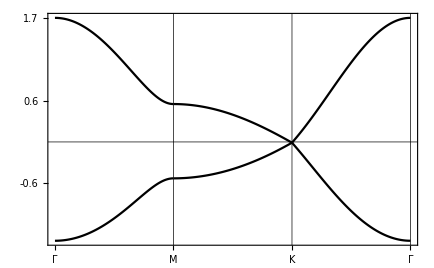

```mathematica
bandplot[path,200,ham,{e1->0.05,r1->0.02,t1->0.5}]
```

```mathematica
sgop=msgop[gray[191]];
init[lattice->{{a,0,0},{-(a/2),(Sqrt[3] a)/2,0},{0,0,c}},lattpar->{a->1,c->3},wyckoffposition->{{{1/3,2/3,0},{0,0,0}}},symminformation->sgop,
basisFunctions->{{"pzup","pzdn"}}];
```

Magnetic space group (BNS): {191.234,P6/mmm1'}

Lattice: HexagonalP

Primitive Lattice Vactor: {{a,0,0},{-a/2,(√3 a)/2,0},{0,0,c}}

Conventional Lattice Vactor: {{a,0,0},{-a/2,(√3 a)/2,0},{0,0,c}}

Double Value Rep.

```mathematica
hamsoc=Sum[symham[n],{n,1,3}];MatrixForm[FullSimplify[hamsoc]]
```

params:{e1}

params:{t1}

params:{r1,r2}

(e1+2 r2 (Cos[kx]+Cos[ky]+Cos[kx+ky])-2 r1 (Sin[kx]+Sin[ky]-Sin[kx+ky]) | 0 | ⅇ^(-1/3 ⅈ (2 kx+ky)) (1+ⅇ^(ⅈ kx)+ⅇ^(ⅈ (kx+ky))) t1 | 0
0 | e1+2 r2 (Cos[kx]+Cos[ky]+Cos[kx+ky])+2 r1 (Sin[kx]+Sin[ky]-Sin[kx+ky]) | 0 | ⅇ^(-1/3 ⅈ (2 kx+ky)) (1+ⅇ^(ⅈ kx)+ⅇ^(ⅈ (kx+ky))) t1
ⅇ^(-1/3 ⅈ (kx+2 ky)) (1+ⅇ^(ⅈ ky)+ⅇ^(ⅈ (kx+ky))) t1 | 0 | e1+2 r2 (Cos[kx]+Cos[ky]+Cos[kx+ky])+2 r1 (Sin[kx]+Sin[ky]-Sin[kx+ky]) | 0
0 | ⅇ^(-1/3 ⅈ (kx+2 ky)) (1+ⅇ^(ⅈ ky)+ⅇ^(ⅈ (kx+ky))) t1 | 0 | e1+2 r2 (Cos[kx]+Cos[ky]+Cos[kx+ky])-2 r1 (Sin[kx]+Sin[ky]-Sin[kx+ky]))

```mathematica
bandManipulate[path,20,hamsoc]
```

Number of params:4

params:{e1,r1,r2,t1}

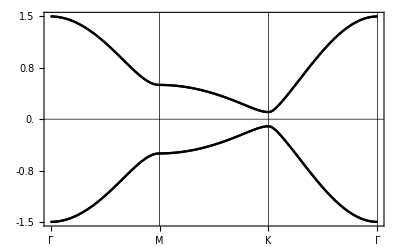

```mathematica
bandplot[path,200,hamsoc,{e1->0,r1->0.02,r2->0,t1->0.5}]
```

```mathematica
hop[hamsoc,{e1->0,r1->0.02,r2->0,t1->0.5}]
```

Generated by MagneticTB
4
7
    1    1    1    1    1    1    1
    -1    -1     0     1     1    0.00000000    0.02000000
    -1    -1     0     2     1    0.00000000    0.00000000
    -1    -1     0     3     1    0.00000000    0.00000000
    -1    -1     0     4     1    0.00000000    0.00000000
    -1    -1     0     1     2    0.00000000    0.00000000
    -1    -1     0     2     2    0.00000000   -0.02000000
    -1    -1     0     3     2    0.00000000    0.00000000
    -1    -1     0     4     2    0.00000000    0.00000000
    -1    -1     0     1     3    0.00000000    0.00000000
    -1    -1     0     2     3    0.00000000    0.00000000
    -1    -1     0     3     3    0.00000000   -0.02000000
    -1    -1     0     4     3    0.00000000    0.00000000
    -1    -1     0     1     4    0.00000000    0.00000000
    -1    -1     0     2     4    0.00000000    0.00000000
    -1    -1     0     3     4    0.00000000    0.00000000
    -1    -1     0     4     4    0.00000000    0.02000000
    -1     0     0     1     1    0.00000000   -0.02000000
    -1     0     0     2     1    0.00000000    0.00000000
    -1     0     0     3     1    0.00000000    0.00000000
    -1     0     0     4     1    0.00000000    0.00000000
    -1     0     0     1     2    0.00000000    0.00000000
    -1     0     0     2     2    0.00000000    0.02000000
    -1     0     0     3     2    0.00000000    0.00000000
    -1     0     0     4     2    0.00000000    0.00000000
    -1     0     0     1     3    0.50000000    0.00000000
    -1     0     0     2     3    0.00000000    0.00000000
    -1     0     0     3     3    0.00000000    0.02000000
    -1     0     0     4     3    0.00000000    0.00000000
    -1     0     0     1     4    0.00000000    0.00000000
    -1     0     0     2     4    0.50000000    0.00000000
    -1     0     0     3     4    0.00000000    0.00000000
    -1     0     0     4     4    0.00000000   -0.02000000
     0    -1     0     1     1    0.00000000   -0.02000000
     0    -1     0     2     1    0.00000000    0.00000000
     0    -1     0     3     1    0.50000000    0.00000000
     0    -1     0     4     1    0.00000000    0.00000000
     0    -1     0     1     2    0.00000000    0.00000000
     0    -1     0     2     2    0.00000000    0.02000000
     0    -1     0     3     2    0.00000000    0.00000000
     0    -1     0     4     2    0.50000000    0.00000000
     0    -1     0     1     3    0.00000000    0.00000000
     0    -1     0     2     3    0.00000000    0.00000000
     0    -1     0     3     3    0.00000000    0.02000000
     0    -1     0     4     3    0.00000000    0.00000000
     0    -1     0     1     4    0.00000000    0.00000000
     0    -1     0     2     4    0.00000000    0.00000000
     0    -1     0     3     4    0.00000000    0.00000000
     0    -1     0     4     4    0.00000000   -0.02000000
     0     0     0     1     1    0.00000000    0.00000000
     0     0     0     2     1    0.00000000    0.00000000
     0     0     0     3     1    0.50000000    0.00000000
     0     0     0     4     1    0.00000000    0.00000000
     0     0     0     1     2    0.00000000    0.00000000
     0     0     0     2     2    0.00000000    0.00000000
     0     0     0     3     2    0.00000000    0.00000000
     0     0     0     4     2    0.50000000    0.00000000
     0     0     0     1     3    0.50000000    0.00000000
     0     0     0     2     3    0.00000000    0.00000000
     0     0     0     3     3    0.00000000    0.00000000
     0     0     0     4     3    0.00000000    0.00000000
     0     0     0     1     4    0.00000000    0.00000000
     0     0     0     2     4    0.50000000    0.00000000
     0     0     0     3     4    0.00000000    0.00000000
     0     0     0     4     4    0.00000000    0.00000000
     0     1     0     1     1    0.00000000    0.02000000
     0     1     0     2     1    0.00000000    0.00000000
     0     1     0     3     1    0.00000000    0.00000000
     0     1     0     4     1    0.00000000    0.00000000
     0     1     0     1     2    0.00000000    0.00000000
     0     1     0     2     2    0.00000000   -0.02000000
     0     1     0     3     2    0.00000000    0.00000000
     0     1     0     4     2    0.00000000    0.00000000
     0     1     0     1     3    0.50000000    0.00000000
     0     1     0     2     3    0.00000000    0.00000000
     0     1     0     3     3    0.00000000   -0.02000000
     0     1     0     4     3    0.00000000    0.00000000
     0     1     0     1     4    0.00000000    0.00000000
     0     1     0     2     4    0.50000000    0.00000000
     0     1     0     3     4    0.00000000    0.00000000
     0     1     0     4     4    0.00000000    0.02000000
     1     0     0     1     1    0.00000000    0.02000000
     1     0     0     2     1    0.00000000    0.00000000
     1     0     0     3     1    0.50000000    0.00000000
     1     0     0     4     1    0.00000000    0.00000000
     1     0     0     1     2    0.00000000    0.00000000
     1     0     0     2     2    0.00000000   -0.02000000
     1     0     0     3     2    0.00000000    0.00000000
     1     0     0     4     2    0.50000000    0.00000000
     1     0     0     1     3    0.00000000    0.00000000
     1     0     0     2     3    0.00000000    0.00000000
     1     0     0     3     3    0.00000000   -0.02000000
     1     0     0     4     3    0.00000000    0.00000000
     1     0     0     1     4    0.00000000    0.00000000
     1     0     0     2     4    0.00000000    0.00000000
     1     0     0     3     4    0.00000000    0.00000000
     1     0     0     4     4    0.00000000    0.02000000
     1     1     0     1     1    0.00000000   -0.02000000
     1     1     0     2     1    0.00000000    0.00000000
     1     1     0     3     1    0.00000000    0.00000000
     1     1     0     4     1    0.00000000    0.00000000
     1     1     0     1     2    0.00000000    0.00000000
     1     1     0     2     2    0.00000000    0.02000000
     1     1     0     3     2    0.00000000    0.00000000
     1     1     0     4     2    0.00000000    0.00000000
     1     1     0     1     3    0.00000000    0.00000000
     1     1     0     2     3    0.00000000    0.00000000
     1     1     0     3     3    0.00000000    0.02000000
     1     1     0     4     3    0.00000000    0.00000000
     1     1     0     1     4    0.00000000    0.00000000
     1     1     0     2     4    0.00000000    0.00000000
     1     1     0     3     4    0.00000000    0.00000000
     1     1     0     4     4    0.00000000   -0.02000000

### Magnetic C-3 Weyl point

```mathematica
sgop=msgop[bnsdict[{143,3}]];
init[lattice->{{(√3)/2,-1/2,0},{0,1,0},{0,0,2}},
lattpar->{},
wyckoffposition->{{{0,0,0},{0,0,1}}},
symminformation->sgop,
basisFunctions->{{{x+ I y,0},{0,x- I y}}}];
c3w=Sum[symham[i],{i,{2,4}}];
c3w2band=Table[c3w[[i,j]],{i,{1,4}},{j,{1,4}}];
```

Magnetic space group (BNS): {143.3,P_c3}

Lattice: HexagonalP

Primitive Lattice Vactor: {{a,0,0},{-a/2,(√3 a)/2,0},{0,0,c}}

Conventional Lattice Vactor: {{a,0,0},{-a/2,(√3 a)/2,0},{0,0,c}}

Double Value Rep.

params:{t1,t10,t11,t12,t13,t14,t15,t16,t2,t3,t4,t5,t6,t7,t8,t9}

params:{s1,s2,s3,s4,s5,s6,s7,s8}

```mathematica
path={{{{0,0,0},{1/2,0,0}},{"\\Gamma","M"}},{{{1/2,0,0},{1/3,1/3,0}},{"M","K"}},{{{1/3,1/3,0},{0,0,0}},{"K","\\Gamma"}},{{{0,0,0},{0,0,1/2}},{"\\Gamma","A"}},{{{0,0,1/2},{1/2,0,1/2}},{"A","L"}},{{{1/2,0,1/2},{1/3,1/3,1/2}},{"L","H"}},{{{1/3,1/3,1/2},{0,0,1/2}},{"H","A"}},{{{1/2,0,1/2},{1/2,0,0}},{"L","M"}},{{{1/3,1/3,0},{1/3,1/3,1/2}},{"K","H"}}};bandManipulate[path,20,c3w2band]
```

Number of params:6

params:{s4,s8,t11,t13,t3,t5}

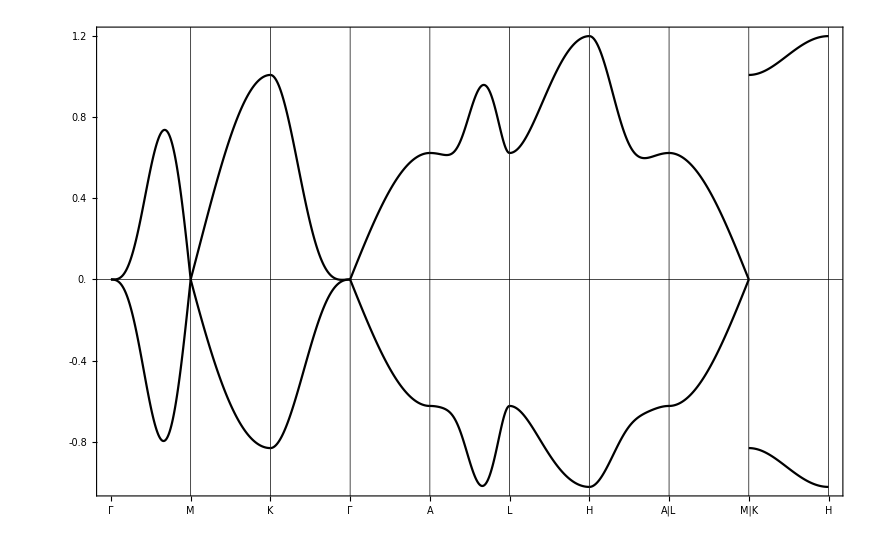

```mathematica
path={{{{0,0,0},{1/2,0,0}},{"\\Gamma","M"}},{{{1/2,0,0},{1/3,1/3,0}},{"M","K"}},{{{1/3,1/3,0},{0,0,0}},{"K","\\Gamma"}},{{{0,0,0},{0,0,1/2}},{"\\Gamma","A"}},{{{0,0,1/2},{1/2,0,1/2}},{"A","L"}},{{{1/2,0,1/2},{1/3,1/3,1/2}},{"L","H"}},{{{1/3,1/3,1/2},{0,0,1/2}},{"H","A"}},{{{1/2,0,1/2},{1/2,0,0}},{"L","M"}},{{{1/3,1/3,0},{1/3,1/3,1/2}},{"K","H"}}};rule=Thread[Variables[c3w2band]->RandomReal[{-1,1},Length@Variables[c3w2band]]];
bandplot[path,200,c3w2band,{s4->-0.15,s8->0.01,t11->-0.246,t13->-0.01,t3->-0.2,t5->0.18}]
```

```mathematica
tt=Normal@Chop@Series[c3w2band,{ky,0,3},{kx,0,3},{kz,0,3}]//Expand;
cub=FromCoefficientRules[Map[Select[#,Total[#[[1]]]==3&]&,CoefficientRules[tt,{kx,ky,kz}],{2}],{kx,ky,kz}];MatrixForm[cub]
```

(2 kx^3 s4-2 ky^3 s4+kx ky^2 (-3 s4+t5)+kx^2 ky (3 s4+t5) | kz^3 (-(ⅈ t11)/24-t3/24)
kz^3 ((ⅈ t11)/24-t3/24) | -2 kx^3 s4+2 ky^3 s4+kx^2 ky (-3 s4-t5)+kx ky^2 (3 s4-t5))

```mathematica
α(kx+ ky)^3+β(kx- ky)^3//Expand
```

kx^3 α+3 kx^2 ky α+3 kx ky^2 α+ky^3 α+kx^3 β-3 kx^2 ky β+3 kx ky^2 β-ky^3 β

```mathematica
2s4(kx+ I ky)^3-(2 kx^3 s4-2 ky^3 s4+kx ky^2 (-3 s4+t5)+kx^2 ky (3 s4+t5))//Expand
```

(-3+6 ⅈ) kx^2 ky s4-3 kx ky^2 s4+(2-2 ⅈ) ky^3 s4-kx^2 ky t5-kx ky^2 t5

```mathematica
SolveAlways[2 kx^3 s4-2 ky^3 s4+kx ky^2 (-3 s4+t5)+kx^2 ky (3 s4+t5)==(c+I d)( kx+Exp[-I Pi/3] ky)^3 +(c-I d)( kx+Exp[I Pi/3] ky)^3,{kx,ky,kz}]
```

{{t5→-3 (-(-1)^(1/6)+(-1)^(5/6)) d+3 (1-(-1)^(1/3)+(-1)^(2/3)) s4,c→s4}}

### Magnetic cubic nodal line

```mathematica
sgop=msgop[bnsdict[{184,196}]];
```

Magnetic space group (BNS): {184.196,P_c6cc}

Lattice: HexagonalP

Primitive Lattice Vactor: {{a,0,0},{-a/2,(√3 a)/2,0},{0,0,c}}

Conventional Lattice Vactor: {{a,0,0},{-a/2,(√3 a)/2,0},{0,0,c}}

```mathematica
init[lattice->{{(√3)/2,-1/2,0},{0,1,0},{0,0,2}},
lattpar->{},
wyckoffposition->{{{0,0,0},{0,0,1}}},
symminformation->sgop,
basisFunctions->{{{x+ I y,0},{0,x- I y}}}]
```

Double Value Rep.

```mathematica
cnl=Sum[symham[i,symmetryset->{2,7,13}],{i,1,5}];
cnl2band=Table[cnl[[i,j]],{i,{1,4}},{j,{1,4}}];MatrixForm[cnl2band]
```

params:{e1,e2}

params:{t1,t2,t3,t4,t5}

params:{r1,r2,r3,r4}

params:{s1,s2,s3}

params:{p5n1,p5n2,p5n3,p5n4,p5n5,p5n6,p5n7,p5n8,p5n9}

(e2+ⅇ^(-ⅈ kz) p5n6+ⅇ^(ⅈ kz) p5n6+ⅇ^(-2 ⅈ kx) p5n9+ⅇ^(2 ⅈ kx) p5n9+ⅇ^(ⅈ (-2 kx-2 ky)) p5n9+ⅇ^(-2 ⅈ ky) p5n9+ⅇ^(2 ⅈ ky) p5n9+ⅇ^(ⅈ (2 kx+2 ky)) p5n9+ⅇ^(ⅈ (-kx-2 ky)) s3+ⅇ^(ⅈ (-2 kx-ky)) s3+ⅇ^(ⅈ (kx-ky)) s3+ⅇ^(ⅈ (-kx+ky)) s3+ⅇ^(ⅈ (2 kx+ky)) s3+ⅇ^(ⅈ (kx+2 ky)) s3+ⅇ^(-ⅈ kx) t4+ⅇ^(ⅈ kx) t4+ⅇ^(ⅈ (-kx-ky)) t4+ⅇ^(-ⅈ ky) t4+ⅇ^(ⅈ ky) t4+ⅇ^(ⅈ (kx+ky)) t4 | ⅇ^(ⅈ (-kx-2 ky-kz/2)) p5n4-ⅇ^(ⅈ (-2 kx-ky-kz/2)) p5n4-ⅇ^(ⅈ (kx-ky-kz/2)) p5n4+ⅇ^(ⅈ (-kx+ky-kz/2)) p5n4+ⅇ^(ⅈ (2 kx+ky-kz/2)) p5n4-ⅇ^(ⅈ (kx+2 ky-kz/2)) p5n4+ⅇ^(ⅈ (-kx-2 ky+kz/2)) p5n4-ⅇ^(ⅈ (-2 kx-ky+kz/2)) p5n4-ⅇ^(ⅈ (kx-ky+kz/2)) p5n4+ⅇ^(ⅈ (-kx+ky+kz/2)) p5n4+ⅇ^(ⅈ (2 kx+ky+kz/2)) p5n4-ⅇ^(ⅈ (kx+2 ky+kz/2)) p5n4+ⅈ ⅇ^(ⅈ (-kx-kz/2)) r1-ⅈ ⅇ^(ⅈ (kx-kz/2)) r1+ⅈ ⅇ^(ⅈ (-ky-kz/2)) r1-ⅈ ⅇ^(ⅈ (-kx-ky-kz/2)) r1-ⅈ ⅇ^(ⅈ (ky-kz/2)) r1+ⅈ ⅇ^(ⅈ (kx+ky-kz/2)) r1+ⅈ ⅇ^(ⅈ (-kx+kz/2)) r1-ⅈ ⅇ^(ⅈ (kx+kz/2)) r1+ⅈ ⅇ^(ⅈ (-ky+kz/2)) r1-ⅈ ⅇ^(ⅈ (-kx-ky+kz/2)) r1-ⅈ ⅇ^(ⅈ (ky+kz/2)) r1+ⅈ ⅇ^(ⅈ (kx+ky+kz/2)) r1
-ⅇ^(ⅈ (-kx-2 ky-kz/2)) p5n4+ⅇ^(ⅈ (-2 kx-ky-kz/2)) p5n4+ⅇ^(ⅈ (kx-ky-kz/2)) p5n4-ⅇ^(ⅈ (-kx+ky-kz/2)) p5n4-ⅇ^(ⅈ (2 kx+ky-kz/2)) p5n4+ⅇ^(ⅈ (kx+2 ky-kz/2)) p5n4-ⅇ^(ⅈ (-kx-2 ky+kz/2)) p5n4+ⅇ^(ⅈ (-2 kx-ky+kz/2)) p5n4+ⅇ^(ⅈ (kx-ky+kz/2)) p5n4-ⅇ^(ⅈ (-kx+ky+kz/2)) p5n4-ⅇ^(ⅈ (2 kx+ky+kz/2)) p5n4+ⅇ^(ⅈ (kx+2 ky+kz/2)) p5n4+ⅈ ⅇ^(ⅈ (-kx-kz/2)) r1-ⅈ ⅇ^(ⅈ (kx-kz/2)) r1+ⅈ ⅇ^(ⅈ (-ky-kz/2)) r1-ⅈ ⅇ^(ⅈ (-kx-ky-kz/2)) r1-ⅈ ⅇ^(ⅈ (ky-kz/2)) r1+ⅈ ⅇ^(ⅈ (kx+ky-kz/2)) r1+ⅈ ⅇ^(ⅈ (-kx+kz/2)) r1-ⅈ ⅇ^(ⅈ (kx+kz/2)) r1+ⅈ ⅇ^(ⅈ (-ky+kz/2)) r1-ⅈ ⅇ^(ⅈ (-kx-ky+kz/2)) r1-ⅈ ⅇ^(ⅈ (ky+kz/2)) r1+ⅈ ⅇ^(ⅈ (kx+ky+kz/2)) r1 | e2+ⅇ^(-ⅈ kz) p5n6+ⅇ^(ⅈ kz) p5n6+ⅇ^(-2 ⅈ kx) p5n9+ⅇ^(2 ⅈ kx) p5n9+ⅇ^(ⅈ (-2 kx-2 ky)) p5n9+ⅇ^(-2 ⅈ ky) p5n9+ⅇ^(2 ⅈ ky) p5n9+ⅇ^(ⅈ (2 kx+2 ky)) p5n9+ⅇ^(ⅈ (-kx-2 ky)) s3+ⅇ^(ⅈ (-2 kx-ky)) s3+ⅇ^(ⅈ (kx-ky)) s3+ⅇ^(ⅈ (-kx+ky)) s3+ⅇ^(ⅈ (2 kx+ky)) s3+ⅇ^(ⅈ (kx+2 ky)) s3+ⅇ^(-ⅈ kx) t4+ⅇ^(ⅈ kx) t4+ⅇ^(ⅈ (-kx-ky)) t4+ⅇ^(-ⅈ ky) t4+ⅇ^(ⅈ ky) t4+ⅇ^(ⅈ (kx+ky)) t4)

```mathematica
path={{{{0,1/10,1/4},{0,0,1/4}},{"Q","P"}},{{{0,0,1/4},{-1/10,1/15,1/4}},{"P","Q"}}};
bandManipulate[path,100,cnl2band]
```

Number of params:7

params:{e2,p5n4,p5n6,p5n9,r1,s3,t4}

### C4 TI

```mathematica
sgop=msgop[gray[75]];
```

Magnetic space group (BNS): {75.2,P41'}

Lattice: TetragonalP

Primitive Lattice Vactor: {{a,0,0},{0,a,0},{0,0,c}}

Conventional Lattice Vactor: {{a,0,0},{0,a,0},{0,0,c}}

```mathematica
init[lattice->{{a,0,0},{0,a,0},{0,0,c}},
lattpar->{a->1,c->1},
wyckoffposition->{{{0,0,1/4},{0,0,0}},{{0,0,0},{0,0,0}}},
symminformation->sgop,
basisFunctions->{{"px","py"},{"px","py"}}]
```

```mathematica
hc4=FullSimplify[
(symham[2]/.{t1->0,t2->t1p})+
(symham[3]/.{r1->0,r2->tzp})+
(symham[4]/.{s10->0,s7->0,s9->0,s2->0,s4->0,s1->0,s6->0,s5->0}/.{s8->t1a,s3->t1b})+
(symham[5]/.{p5n2->0,p5n3->0,p5n1->p5n4}/.{p5n4->t2p})+
(symham[7]/.{p7n7->p7n5,p7n1->0,p7n4->0,p7n2->0,p7n3->0,p7n14->p7n12,p7n11->0,p7n8->0,p7n10->0,p7n9->0,p7n6->-p7n5,p7n13->p7n12}/.{p7n5->t2a/2,p7n12->t2b/2})]
```

params:{t1,t2}

params:{r1,r2}

params:{s1,s10,s2,s3,s4,s5,s6,s7,s8,s9}

params:{p5n1,p5n2,p5n3,p5n4}

params:{p7n1,p7n10,p7n11,p7n12,p7n13,p7n14,p7n2,p7n3,p7n4,p7n5,p7n6,p7n7,p7n8,p7n9}

{{2 Cos[kx] (t1a+t2a Cos[ky]),2 t2a Sin[kx] Sin[ky],ⅇ^(-1/4 ⅈ (4 (kx+ky)+kz)) (t1p+ⅇ^(ⅈ kz) tzp+2 t2p (Cos[kx]+Cos[ky])) (Cos[kx+ky]+ⅈ Sin[kx+ky]),0},{2 t2a Sin[kx] Sin[ky],2 (t1a+t2a Cos[kx]) Cos[ky],0,ⅇ^(-1/4 ⅈ (4 (kx+ky)+kz)) (t1p+ⅇ^(ⅈ kz) tzp+2 t2p (Cos[kx]+Cos[ky])) (Cos[kx+ky]+ⅈ Sin[kx+ky])},{ⅇ^(-1/4 ⅈ (4 (kx+ky)+3 kz)) (tzp Cos[kx+ky]+ⅈ tzp Sin[kx+ky]+(t1p+2 t2p (Cos[kx]+Cos[ky])) (Cos[kx+ky+kz]+ⅈ Sin[kx+ky+kz])),0,2 Cos[kx] (t1b+t2b Cos[ky]),2 t2b Sin[kx] Sin[ky]},{0,ⅇ^(-1/4 ⅈ (4 (kx+ky)+3 kz)) (tzp Cos[kx+ky]+ⅈ tzp Sin[kx+ky]+(t1p+2 t2p (Cos[kx]+Cos[ky])) (Cos[kx+ky+kz]+ⅈ Sin[kx+ky+kz])),2 t2b Sin[kx] Sin[ky],2 (t1b+t2b Cos[kx]) Cos[ky]}}

```mathematica
path={{{{0,0,0},{1/2,1/2,0}},{"Γ","M"}},{{{1/2,1/2,0},{1/2,1/2,1/2}},{"M","A"}},{{{1/2,1/2,1/2},{0,0,1/2}},{"A","Z"}},{{{0,0,1/2},{0,0,0}},{"Z","Γ"}}};
```

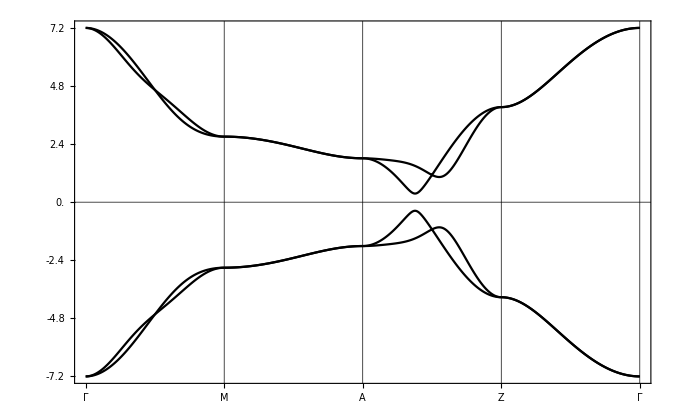

```mathematica
bandplot[path,200,hc4,{t1a->1,t1b->-1,t2a->0.5,t2b->-0.5,t1p->2.5,t2p->.5,tzp->2}]
```

```mathematica
fumodel=ExpToTrig@symhamII[hc4];MatrixForm[fumodel]
```

(2 t1a Cos[kx]+t2a Cos[kx-ky]+t2a Cos[kx+ky] | t2a Cos[kx-ky]-t2a Cos[kx+ky] | t1p+2 t2p Cos[kx]+2 t2p Cos[ky]+tzp Cos[kz]+ⅈ tzp Sin[kz] | 0
t2a Cos[kx-ky]-t2a Cos[kx+ky] | t2a Cos[kx-ky]+2 t1a Cos[ky]+t2a Cos[kx+ky] | 0 | t1p+2 t2p Cos[kx]+2 t2p Cos[ky]+tzp Cos[kz]+ⅈ tzp Sin[kz]
t1p+2 t2p Cos[kx]+2 t2p Cos[ky]+tzp Cos[kz]-ⅈ tzp Sin[kz] | 0 | 2 t1b Cos[kx]+t2b Cos[kx-ky]+t2b Cos[kx+ky] | t2b Cos[kx-ky]-t2b Cos[kx+ky]
0 | t1p+2 t2p Cos[kx]+2 t2p Cos[ky]+tzp Cos[kz]-ⅈ tzp Sin[kz] | t2b Cos[kx-ky]-t2b Cos[kx+ky] | t2b Cos[kx-ky]+2 t1b Cos[ky]+t2b Cos[kx+ky])